```mathematica
<<PCA.m

faces = LoadFaces[100];
flatFaces = FlattenImage /@ faces;
```

```mathematica
eigenfaces = EigenFaces[faces, 200]
```

{{0.00900155,0.00896625,0.00911912,0.0096342,0.00983591,0.0100742,9989,0.00216064,0.00238967,0.00228396,0.00290217,0.00277022},198,{1}}
 |  |  |  |

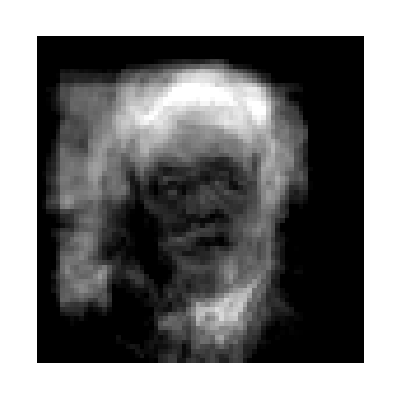
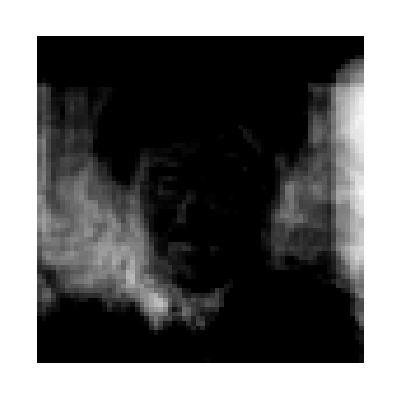
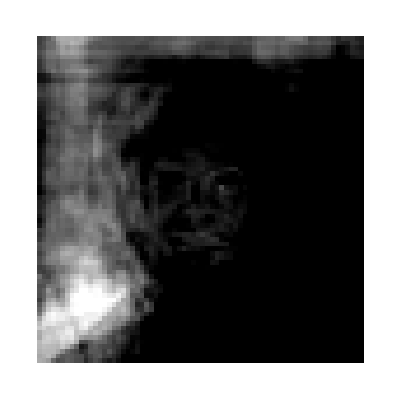
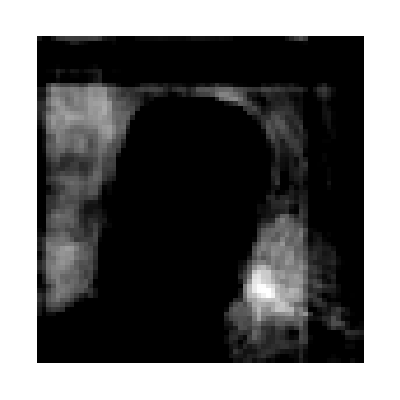
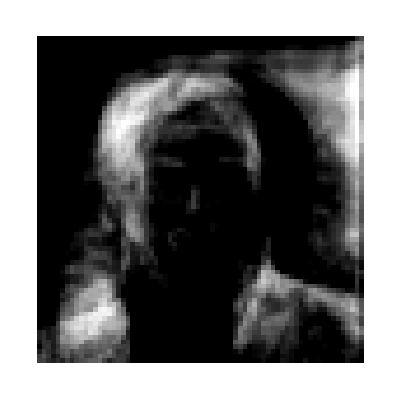
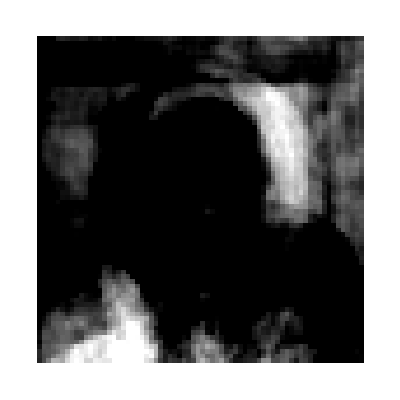
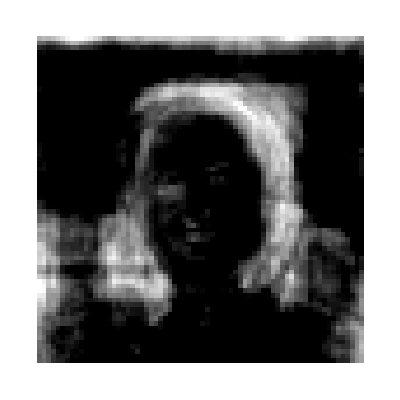
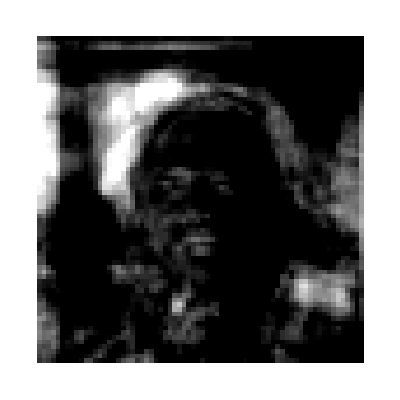

```mathematica
FormatFace /@ (-30 * eigenfaces[[3;;10]])
```

```mathematica
avg = N[Total[flatFaces]]/Length[flatFaces];
```

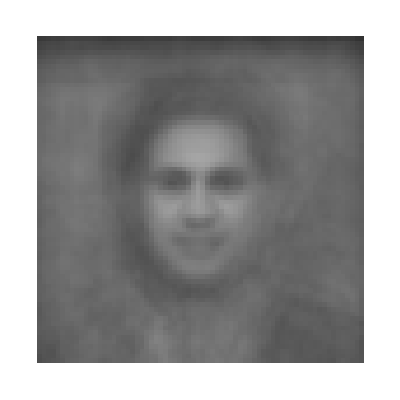

```mathematica
(FormatFace /@ (Function[x,avg ] /@ eigenfaces))[[1]]
```

```mathematica
face = FlattenImage[faces[[1]]];
```

```mathematica
decon = eigenfaces.face;
```

```mathematica
recon = Transpose[eigenfaces].decon;
```

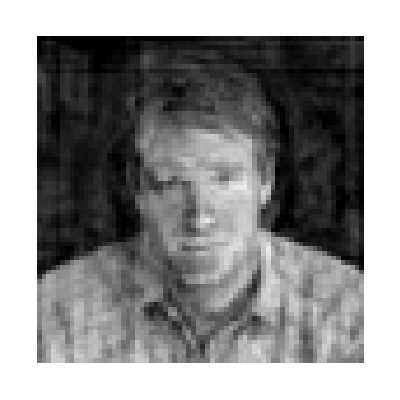

```mathematica
FormatFace[Function[x,  x + avg/5] @ recon]
```

1

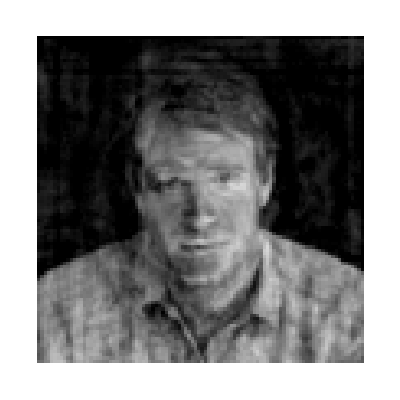

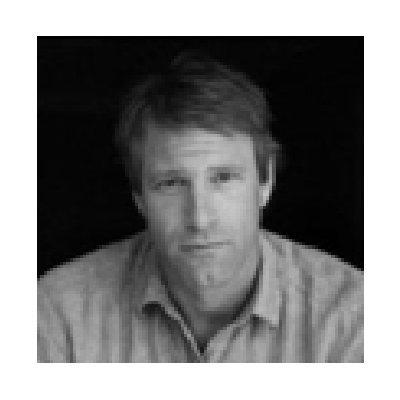

```mathematica
n = 1
FormatFace[Transpose[eigenfaces].eigenfaces.FlattenImage[faces[[n]]]]

FormatFace[FlattenImage[faces[[n]]]]
```

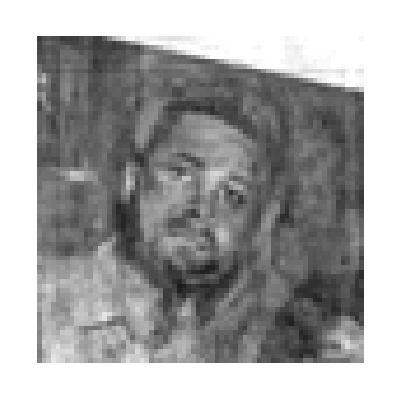

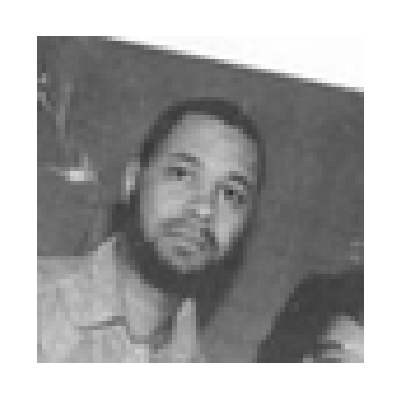

```mathematica
4
```

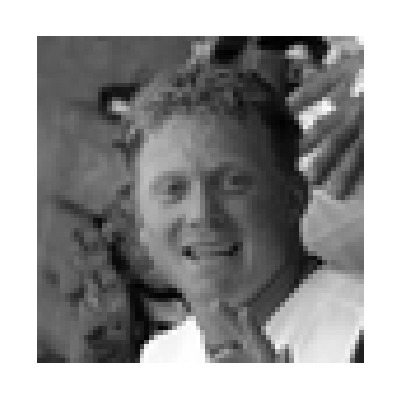

```mathematica
FormatFace[FlattenImage[faces[[2]]]]
```

```mathematica
(Transpose[eigenfaces].eigenfaces)[[1;;5,1;;5]]
```

{{0.0306496,0.0271289,0.020992,0.0170361,0.0155142},{0.0271289,0.0259699,0.0221452,0.017859,0.0164781},{0.020992,0.0221452,0.02511,0.0213,0.0196922},{0.0170361,0.017859,0.0213,0.0253379,0.0258893},{0.0155142,0.0164781,0.0196922,0.0258893,0.0280902}}

```mathematica
Dot[Transpose[eigenfaces], eigenfaces]
```

{{12.0013,11.9019,11.9303,12.0268,11.9634,11.933,4888,6.86694,7.08463,7.40371,7.56042,7.93386,8.05686},4898,{1}}
 |  |  |  |

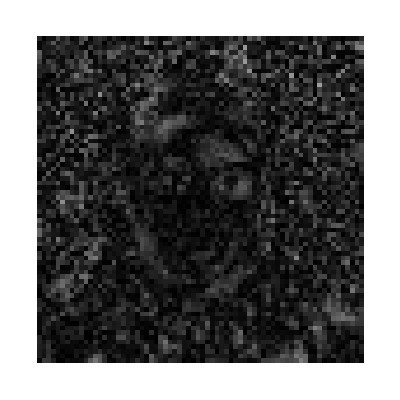

```mathematica
FormatFace[1.5 * Abs /@ (Transpose[eigenfaces].(Table[Random[], {i, 1,200}]))]
```

```mathematica
Export["larger_eigenfaces.csv", eigenfaces, "CSV"]
```

larger_eigenfaces.csv